# Gauss-Jordan Elimination

## Jacob Russell

```mathematica
(* Gauss-Jordan elimination module *)
```

```mathematica
gaussJordan[A_,B_]:=Module[{n ,ab,temp,w}, 
n =Length[Transpose[A]];
w =Length[Transpose[B]];
ab=ArrayFlatten[{{A,B}}];

(* Forward elimination *)
For[i=1,i<=n-1,i++,

       (* Here we deal with row switching in case our pivot is 0 *)
       (* The sorting algorithm used is Bubble Sort with O(n^2) time *)
        For[s=i+1,s<=n,s++,
	        If[Abs[ab⟦i,i⟧]<Abs[ab⟦s,i⟧],
		  temp = ab⟦i⟧;
		  ab⟦i⟧=ab⟦s⟧;
		  ab⟦s⟧=temp;
             ];
 
         For[k=i+1,k<=n,k++,
		(* Here we are making sure we do not divide by 0 by skipping an element if it is already 0 *)
		If[Abs[ab⟦i,i⟧]<$MachineEpsilon, Break[];];

	          ab⟦k⟧+=(-ab⟦k,i⟧/ab⟦i,i⟧)*ab⟦i⟧
];
];
];
(* Backward elimination *)
For[i=n,i>=2,i--,
	For[k=i-1,k>=1,k--,
		(* Here we are making sure we do not divide by 0 when we are backward eliminating *)
		If[Abs[ab⟦i,i⟧]<$MachineEpsilon && Abs[ab⟦i,n+1⟧]<$MachineEpsilon,
		     Print["Infinitely many solutions."]; (* if an entire row is 0s then we have... *)
		     Print[ab];
		     Abort[];
                ];
		If[Abs[ab⟦i,i⟧]<$MachineEpsilon&&Abs[ab⟦i,n+1⟧]>$MachineEpsilon,
                      Print["No solution."]; (* if we have all 0s in a row except the last element we have... *)
		    Print[ab];
		    Abort[];
	       ];
	       (* Otherwise we continue *)
		      ab⟦k⟧=(-ab⟦k,i⟧)/ab⟦i,i⟧ab⟦i⟧+ab⟦k⟧;
];
];

(* Normalize the diagonal *)
For[x=1,x≤n,x++,
	ab⟦x⟧=ab⟦x⟧/ab⟦x,x⟧;
]; 

(* This return statement will also allow us to find the inverse of A
  by making B the nxn identity matrix *)
Return [Table[ab⟦i,j⟧,{i,1,n},{j,n+1,n+w}]]; 
]
```

## 1)

```mathematica
A=({{2, 1, 0}, {1, -11, 4.2}, {3, 17.1, -5}});
B=({{-5.6}, {2.4}, {2.9}});
gaussJordan[A,B]
```

{{-7.3798},{9.1596},{26.318}}

## 2)

```mathematica
A=({{10^(-19), 0, .03, 2}, {10^(-19), .01, 0, 4}, {.01, 1, 0, 0}, {0, 0, 6, 2}});
```

```mathematica
B=Table[{i},{i,4}];
```

```mathematica
gaussJordan[A,B]
```

{{-1.50754},{3.01508},{0.502513},{0.492462}}

## 3)

```mathematica
A=Table[i,{i,5},{i,5}];
B=Table[{i},{i,5}];
```

```mathematica
gaussJordan[A,B]
```

No solution.

{{1,2,3,4,5,1},{0,0,0,0,0,1},{0,0,0,0,0,2},{0,0,0,0,0,3},{0,0,0,0,0,4}}

$Aborted

## 4)

```mathematica
A=Table[i,{i,5},{i,5}];
```

```mathematica
B=Table[{1},{i,5}];
```

```mathematica
gaussJordan[A,B]
```

Infinitely many solutions.

{{1,2,3,4,5,1},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

$Aborted

## 5)

```mathematica
A = RandomReal[{-10,10},{5,5}];
```

```mathematica
B=RandomReal[{-10,10},{5,1}];
```

```mathematica
LinearSolve[A,B]
```

{{-1.53246},{1.35598},{1.31128},{2.66925},{-0.156252}}

```mathematica
gaussJordan[A,B]
```

{{-1.53246},{1.35598},{1.31128},{2.66925},{-0.156252}}

## 6)

```mathematica
A=IdentityMatrix[5];
```

```mathematica
B=RandomReal[{-10,10},{5,1}];
```

```mathematica
Inverse[B]
```

Inverse[{{0.35174},{6.74629},{3.96086},{-8.53409},{2.82099}}]

```mathematica
gaussJordan[A,B]
```

{{0.35174},{6.74629},{3.96086},{-8.53409},{2.82099}}

## 7) Application

```mathematica
(* Define given values of xs and ys. *)
```

```mathematica
xvals=Table[w,{w,.25,3.,.25}];
```

```mathematica
yvals ={{0.24740395925452294},{0.479425538604203},{0.6816387600233341},{0.8414709848078965},{0.9489846193555862},{0.9974949866040544},{0.9839859468739369},{0.9092974268256817},{0.7780731968879212},{0.5984721441039564},{0.3816609920523317},{0.1411200080598672}};
```

```mathematica
XY=Table[{xvals[[i]],yvals[[i,1]]},{i,1,Length[xvals]}];
```

```mathematica
(* Construct the design matrix A *)
```

```mathematica
A=Table[xvals⟦i⟧^k,{i,1,12},{k,0,11,1}];
```

```mathematica
B=yvals;
```

```mathematica
(* Find coefficients using gaussJordan *)
```

```mathematica
coefficients=Flatten[gaussJordan[A,B]]
```

```mathematica
{-5.762504667883306*^-8,1.000000714504325,-3.7078742328722214*^-6,-0.16665583418459048,-0.00002007208679950523,0.008358385599268103,-0.00002171702601638422,-0.00018519443376790234,-5.6086164220875845*^-6,4.3648073002600865*^-6,-2.8957501739724745*^-7,1.3188962021434724*^-9}
```

```mathematica
(* Construct polynomial - this is the least degree polynomial which pass through the given points. *)
```

```mathematica
f[h_]=h^(Range[Length[coefficients]]-1).coefficients
```

-5.7625×10^-8+1. h-3.70787×10^-6 h^2-0.166656 h^3-0.0000200721 h^4+0.00835839 h^5-0.000021717 h^6-0.000185194 h^7-5.60862×10^-6 h^8+4.36481×10^-6 h^9-2.89575×10^-7 h^10+1.3189×10^-9 h^11

```mathematica
(* Showing interpolation graphically *)
```

```mathematica
fp=Plot[f[h],{h,0.25,3},PlotRange->{Min[yvals]-2,Max[yvals]+2}];
```

```mathematica
lp=ListPlot[XY,AxesOrigin->{0,0},PlotRange->{Min[yvals]-2,Max[yvals]+2}];
```

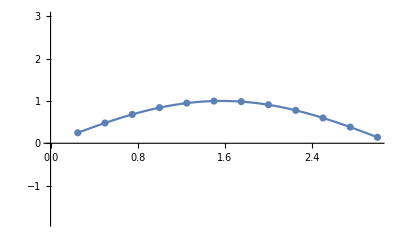

```mathematica
Show[fp,lp]
```